```mathematica
ImageCompose
```

```mathematica
覆盖图像是部分透明的
```

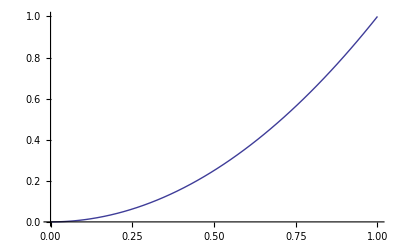
```mathematica
ImageCompose[-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
指定一个明确的位置覆盖：
后面的两个坐标均以直角坐标系为准，分别作为两个图像的坐标，前面的坐标表示后图，后者表示前图.
```

```mathematica
ImageCompose[-Graphics-,-Graphics-,{100,30},{0,0}]
```

-Graphics-

```mathematica
Graphics[Text[Style["Mathematics",Large]],ImageSize->{130,20}]
```

-Graphics-

```mathematica
指定一个alpha-blending参数：半透明参数
```

```mathematica
ImageCompose[-Graphics-, {Graphics[{Yellow,Disk[]}], 0.5}]
```

-Graphics-

```mathematica
创建一个动态模糊效果：
```

```mathematica
Nest[ ImageCompose[#,{#,0.1}, {1,0},{0,0}]&, -Graphics-, 50]
```

-Graphics-

```mathematica
全方位探讨alpha-compositing模式和参数：
```

```mathematica
Manipulate[Row[ {ImageCompose[ -Graphics-,-Graphics-,{fob,fim,mode}],{Round[fob],Round[fim],mode} /. { {1,0,1}-> "object",{0,1,-1}-> "image", {1, 1,1}->"object over image",  {1,1,-1}-> "image over object", {0,0,1}-> "object in image", {0,0,-1}-> "image in object",{1,0,0}-> "object out image",{0,1,0}-> "image out object",{0,1,1}-> "object atop image",{1,0,-1}-> "image atop object",{0,0,0}-> "clear",{1,1,0}-> "object xor image",  _-> "" }}],{{mode,1},{1->"object",-1->"image", 0-> "none"}}, {{fob,1},0,1},{{fim,1},0,1}]
```